```mathematica
"grid1=Import["~/Desktop/interpol/grids_1nov/grid4_MI_nint_1nov_1_880x300.dat","Table"];
```

```mathematica
grid1=Import["/home/eduardo/Desktop/trabajo/bethe-salpeter17/salida9.out","Table"];
```

Import::nffil: File not found during Import.

```mathematica
grid1=Import["/home/user/Desktop/trabajo/bethe-salpeter/bethe-salpeter17/salidas/u-mh-1p0-mu1-np128-quad/salida9.out","Table"];
```

```mathematica
grid2=Import["/home/user/Desktop/trabajo/bethe-salpeter/bethe-salpeter17/salidas/u-mh-1p0-mu1-np128-quad/salida3.out","Table"];
```

```mathematica
"grid1=Import["~/Desktop/alr-files/salidas/deltapvdis_1p2TeV.dat","Table"];
```

```mathematica
"grid1=Import["~/Desktop/interpol/grids_1nov/grid4_MI_nint_1nov_3_220x300.dat","Table"];
```

```mathematica
"265181 for range 1, (265041  for range 2, 132821),881x301=66521 for range 3,
```

```mathematica
sigmaB5= Table[{grid1[[i,1]],grid1[[i,2]],grid1[[i,3]]},{i,1,6400}];
```

```mathematica
sigmaB2= Table[{grid2[[i,1]],grid2[[i,2]],grid2[[i,3]]},{i,1,6400}];
```

```mathematica
chi2=Interpolation[sigmaB5]
```

Interpolation::indim: The coordinates do not lie on a structured tensor product grid.

Interpolation[{{-0.0618391,-0.000551477,0.000183909},{-0.0614726,-0.000549841,0.00215987},{-0.0608171,-0.000546901,0.000825358},{-0.0598784,-0.000542665,-0.0000755256},{-0.0586656,-0.000537141,-0.000114526},«4086»,{9.93438,1.53135,-0.0114192},{9.93317,1.5471,-0.0124585},{9.93223,1.55918,-0.01455},{9.93158,1.56756,-0.0193386},{9.93121,1.57223,-0.0253606}}]

```mathematica
Minimize[{chi2[x,y],-1.57079633<x<1.57079633&&-1.57079633<y<1.57079633},{x,y}]
```

{-0.0690182,{x→-1.5708,y→-0.405863}}

```mathematica
"for proton
{-0.0690182473943088`,{x→-1.57079633`,y→-0.4058629878164108`}}
```

```mathematica
"minimum for Cs
{-0.006763129757146015`,{x→0.018100467443672053`,y→0.4505836381829008`}}
for pvdis
{-0.01009242154438313`,{x→1.329744667470993`,y→0.07959058173329205`}}
for E158
{-0.11270320475400905`,{x→-1.57079633`,y→-0.4058635731216355`}}
```

```mathematica
Maximize[{chi2[x,y],-1.57079633<x<1.57079633&&-1.57079633<y<1.57079633},{x,y}]
```

{0.0377602,{x→-0.279962,y→0.560705}}

```mathematica
"maximum for proton 
 {0.03776016590526594`,{x→-0.2799622851544464`,y→0.5607048573404958`}}
```

```mathematica
"maximum for cs
{0.005439992310603482`,{x→1.57079633`,y→0.4058638376487896`}}
for pvdis
{-5.07615073449286`*^-12,{x→0.36384801064596367`,y→1.57079633`}}
for E158
{0.06166038521043133`,{x→-0.27996231418414325`,y→0.5607046578690562`}}
```

```mathematica
Needs["PlotLegends`"]
```

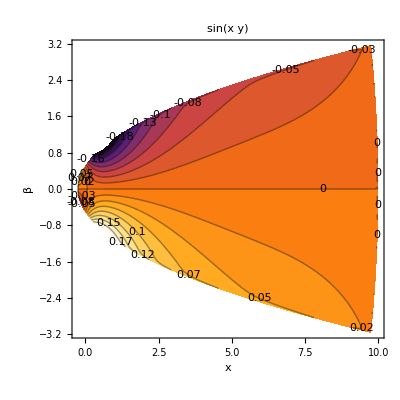

```mathematica
Graphics[ListContourPlot[sigmaB5,ContourLabels->All,ColorFunction->"SunsetColors",PlotRange->{-0.2,0.2},Contours->15,FrameLabel->{x,Style[β,Large,Bold,Blue]},PlotLabel->Sin[x y],Background->White],Text["asfdasfasdfasfasdasdfasdfasdf",{0,1,0}]]
```

```mathematica
ListPlot3D[sigmaB2,PlotRange->All]
```

-Graphics3D-

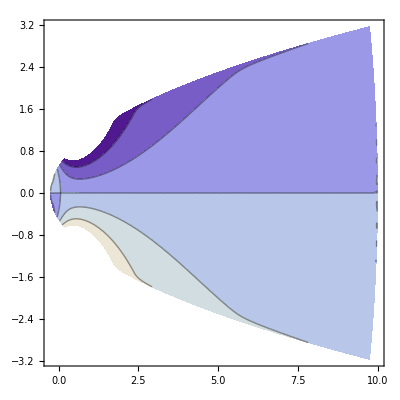

```mathematica
ListContourPlot[sigmaB5]
```

```mathematica
sansonf=Table[{sigmaB5[[i*100+1,1]]*Cos[sigmaB5[[i*100+1,2]]],sigmaB5[[i*100+1,2]],sigmaB5[[i*100+1,3]]},{i,0,10020}];
```

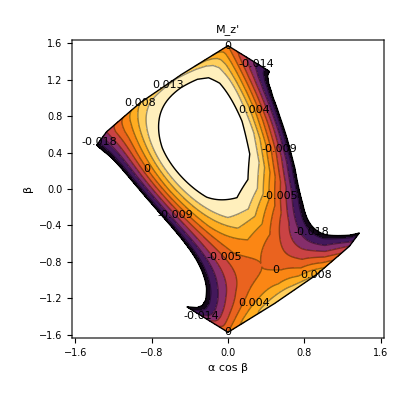

```mathematica
Show[ListContourPlot[sansonf,ContourLabels->All,ColorFunction->"SunsetColors",PlotRange->{-0.0201429,0.0201429},Contours->8,FrameLabel->{Style["α cos β",Large,Bold,Blue],Style[β,Large,Bold,Blue]},PlotLabel->Style[Subscript[M,z'],Large,Bold,Red],BoundaryStyle->Black,Background->White]]
```

```mathematica
Maximize[{chi2[x,y],-1.57079633<x<1.57079633&&-1.57079633<y<1.57079633},{x,y}]
```

{0.168152,{x→-0.279976,y→0.560719}}

```mathematica
1 parameter:set err 1.0000 (68.269% range)
set err 1.6424 (80% range& 90% one-sided limit)
set err 2.7055 (90% range& 95% one-sided limit))
set err 3.8415 (95% range)
set err 6.6349 (99% range)

2 parameters:set err 1.0000 (39.347% region)
set err 2.2958 (68.269% region)
set err 4.6052 (90% region)
set err 5.9915 (95% region)
set err 9.2103 (99% region)
```

```mathematica
"For proton 90%"
0.0712234
-0.0627683
"symmetric case 2sep"
0.0657936
"21 sept 2.1%"
0.0345416
"24 sep 1.2246 %1 combined with MOLLER"
0.0201429
"proton 68%"
-0.0365101
0.0449512
"proton 1.5%"
-0.0246726
+0.0205562
------
"For cs 90%"
-0.00799251
0.00774348
"for cs 68%"
0.00465892
-0.00490796
------
"for pvdis 90%"
-0.00907262
0.0106539
"PVDIS SYMMETRIC"
 0.009863283582046588
"PVDIS 00057"
(0.0057)*Sqrt[2.7055]
"for pvdis 68% do again"
0.00678716
-0.00520584
-----
"for E158 90 do AGAIN%"
0.0373251
-0.331229
"E158 68%"
-0.03491863138509406
-0.258986
```

```mathematica
-------
"Moller 90"
```

```mathematica
0.0378313
-0.0378313
"sept 24 90% combined with Qweak 0.0186844"
0.0307329
"moller 68%"
0.023
-0.23
```

```mathematica
"Moller centered at E158/2"
```

```mathematica
-0.0412041
-0.105748
```

```mathematica
"aa= confidence level + minimum"
```

```mathematica
aa= 0.02
```

0.02

```mathematica
`
```

```mathematica
Do[If[(sigmaB5[[i-1,3]]≤aa&&sigmaB5[[i,3]]≥aa),PutAppend[FortranForm[{sigmaB5[[i-1,1]]+(sigmaB5[[i,1]]-sigmaB5[[i-1,1]])/(sigmaB5[[i,3]]-sigmaB5[[i-1,3]]) (aa-sigmaB5[[i-1,3]]) ,sigmaB5[[i-1,2]]+(sigmaB5[[i,2]]-sigmaB5[[i-1,2]])/(sigmaB5[[i,3]]-sigmaB5[[i-1,3]]) (aa-sigmaB5[[i-1,3]]),sigmaB5[[i-1,3]],sigmaB5[[i,3]]}],"~/Desktop/contour1-0p02.dat"],0];
If[sigmaB5[[i-1,3]]≥aa&&sigmaB5[[i,3]]≤aa,PutAppend[FortranForm[{sigmaB5[[i-1,1]]+(sigmaB5[[i,1]]-sigmaB5[[i-1,1]])/(sigmaB5[[i,3]]-sigmaB5[[i-1,3]]) (aa-sigmaB5[[i-1,3]]) ,sigmaB5[[i-1,2]]+(sigmaB5[[i,2]]-sigmaB5[[i-1,2]])/(sigmaB5[[i,3]]-sigmaB5[[i-1,3]]) (aa-sigmaB5[[i-1,3]]),sigmaB5[[i-1,3]],sigmaB5[[i,3]]}],"~/Desktop/contour2-0p02.dat"],0];,{i,2,4096}]
```

```mathematica
"265181 for range 1, (265041  for range 2 132821), 881x301=66521 for range 3,
```

```mathematica
"Do[PutAppend[FortranForm[{sigmaB5[[i,1]]*Cos[sigmaB5[[i,2]]],sigmaB5[[i,2]]}],"/home/eduardor/Desktop/graficas/graficas-"5abril/border-alpha-plus-pihalf.dat" ],{i,10297,10398}]
```

```mathematica
count=Import["~/Desktop/alr-files/contour-1p2TeV-qweak-2p01Em2-2.dat","Table"];
```

```mathematica
Do[PutAppend[FortranForm[{count[[441-i,1]],count[[441-i,2]]}],"~/Desktop/alr-files/contour-1p2TeV-qweak-2p01Em2-2-inv.dat"] ,{i,0,440}]
```